## Hayes & Adams (2017) Mathematica Notebook 4 Monte Carlos & Model Projections for the MYTH Model for Boulder

This document is a pdf created from a Wolfram Mathematica notebook prepared by Mark A. Hayes during December 2016, following the general approach for logistic regression and Monte Carlo simulations outlined in Hayes (2011). This code and output supports the analysis described in Hayes, M. A. and R. A. Adams. 2017. Simulated bat populations collapse when exposed to conditions that mimic climate change projections for western North America. PLOS ONE. If you would like a copy of the original Mathematica notebook, please contact MAH at hayesm@usgs.gov or hayes.a.mark@gmail.com.  

This uses the model Temp + Precip with beta estimates from the full model. 

Mark A. Hayes
January 19, 2017

### Set the directory

```mathematica
SetDirectory[NotebookDirectory[]]
```

\\IGSKBACBFS2\groups\bts\t\mah\manuscripts\2016\Hayes & Adams 2016 - Bat pop modeling - PLOS ONE\revision - fall winter 2016\Plos One - Data package

#### Deterministic repro rate = 0.85

```mathematica
DetRepro = {0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85,0.85};
```

## “Current Climate”1950-2000 Projections and Simulations

### Model projections using 1950-2000 worldclim average values

```mathematica
ProbCurrentAve = {0.8500,0.8500,0.8500,0.8500,0.8500,0.8500,0.8500,0.8500,0.8499,0.8499,0.8499,0.8499,0.8499,0.8499,0.8499,0.8499,0.8499,0.8499,0.8499,0.8499,0.8499,0.8499,0.8498,0.8498,0.8498,0.8498,0.8498,0.8498,0.8498,0.8498,0.8498,0.8498,0.8498,0.8498,0.8498,0.8498,0.8497,0.8497,0.8497,0.8497,0.8497,0.8497,0.8497,0.8497,0.8497,0.8497,0.8497,0.8497,0.8497,0.8497,0.8496,0.8496,0.8496,0.8496,0.8496,0.8496,0.8496,0.8496,0.8496,0.8496,0.8496,0.8496,0.8496,0.8496,0.8495,0.8495,0.8495,0.8495,0.8495,0.8495,0.8495,0.8495,0.8495,0.8495,0.8495,0.8495,0.8495,0.8495};
Mean[ProbCurrentAve]
```

0.849731

```mathematica
aReproCurrentAve =ProbCurrentAve;
```

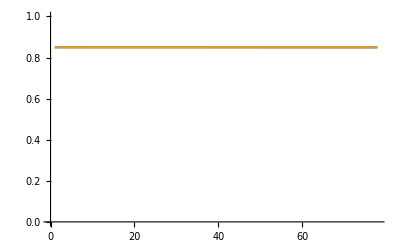

```mathematica
ListLinePlot[{aReproCurrentAve, DetRepro},PlotRange->{0,1}]
```

### Monte Carlo Current simulation

```mathematica
SAave=0.79;
SAmin=SAave*0.90;
SAmax=SAave*1.10;

SFave=SAave*0.64;
SFmin=SFave*0.90;
SFmax=SFave*1.10;

aReproAve=SAave*(aReproCurrentAve/2);
aReproMin=aReproAve*0.90;
aReproMax=aReproAve*1.10;

jReproAve=0.90*(aReproCurrentAve/2)*SFave;
jReproMin=jReproAve*0.90;
jReproMax=jReproAve*1.10;

runs=10000;
j=0;
```

```mathematica
MonteCarlo=Table[Npups=600;Nne=290;Ntwo=230;Nthree=880;
i=1;While[i<77,Ntotal=Npups+Nne+Ntwo+Nthree;
Nthree=(Ntwo*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]))+(Nthree*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Ntwo=(Nne*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Nne=(Npups*(RandomReal[TriangularDistribution[{SFmin,SFmax},SFave]]));
Npups=(Npups*(RandomReal[TriangularDistribution[{jReproMin[[i]],jReproMax[[i]]},jReproAve[[i]]]]))+(Nne*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Ntwo*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Nthree*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]));
i=i+1;];j=j+1;Ntotal,{runs}];k=0;
```

2057.23

418.698

996.

4199.

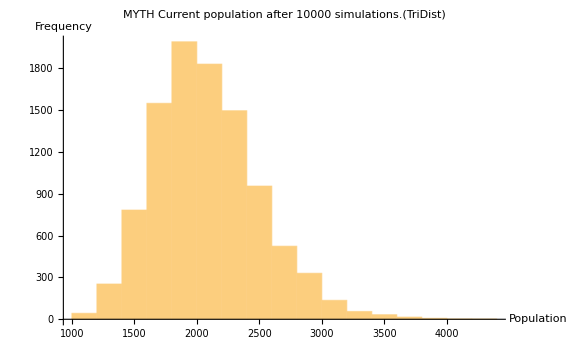

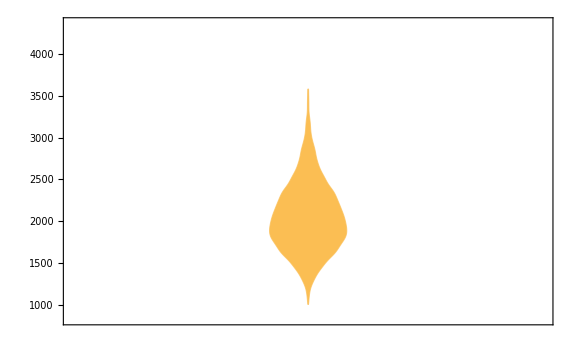

```mathematica
N[Mean[Round[MonteCarlo]]]
N[StandardDeviation[Round[MonteCarlo]]]
N[Min[Round[MonteCarlo]]]
N[Max[Round[MonteCarlo]]]
Hist=Round[MonteCarlo,50];
Histogram[Hist,BaseStyle->{FontSize->14},ImageSize->Large,PlotLabel->StringJoin["MYTH Current population after ",ToString[runs]," simulations.","(TriDist)"],AxesLabel->{"Population","Frequency"}]
DistributionChart[Round[MonteCarlo]]
```

## RCP 2.6 Projections and Simulations

### Model projections using RCP26 2009-2086 average values

Predicted probability of an adult female being reproductively active in a given year, given RCP26 average values for years 2009-2086, using logistic regressiion.

```mathematica
ProbRCP26Ave = {0.8500,0.8500,0.8500,0.8500,0.8500,0.8500,0.8500,0.8500,0.8499,0.8499,0.8499,0.8499,0.8499,0.8499,0.8499,0.8499,0.8499,0.8499,0.8499,0.8499,0.8499,0.8499,0.8498,0.8498,0.8498,0.8498,0.8498,0.8498,0.8498,0.8498,0.8498,0.8498,0.8498,0.8498,0.8498,0.8498,0.8497,0.8497,0.8497,0.8497,0.8497,0.8497,0.8497,0.8497,0.8497,0.8497,0.8497,0.8497,0.8497,0.8497,0.8496,0.8496,0.8496,0.8496,0.8496,0.8496,0.8496,0.8496,0.8496,0.8496,0.8496,0.8496,0.8496,0.8496,0.8495,0.8495,0.8495,0.8495,0.8495,0.8495,0.8495,0.8495,0.8495,0.8495,0.8495,0.8495,0.8495,0.8495};
Mean[ProbRCP26Ave]
```

0.849731

```mathematica
aReproRCP26Ave =ProbRCP26Ave;
```

```mathematica
ListLinePlot[{aReproRCP26Ave, DetRepro},PlotRange->{0,1}]
```

-Graphics-

### Monte Carlo RCP 26 simulation

```mathematica
SAave=0.79;
SAmin=SAave*0.90;
SAmax=SAave*1.10;

SFave=SAave*0.64;
SFmin=SFave*0.90;
SFmax=SFave*1.10;

aReproAve=SAave*(aReproRCP26Ave/2);
aReproMin=aReproAve*0.90;
aReproMax=aReproAve*1.10;

jReproAve=0.90*(aReproRCP26Ave/2)*SFave;
jReproMin=jReproAve*0.90;
jReproMax=jReproAve*1.10;

runs=10000;
j=0;
```

```mathematica
MonteCarlo=Table[Npups=600;Nne=290;Ntwo=230;Nthree=880;
i=1;While[i<77,Ntotal=Npups+Nne+Ntwo+Nthree;
Nthree=(Ntwo*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]))+(Nthree*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Ntwo=(Nne*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Nne=(Npups*(RandomReal[TriangularDistribution[{SFmin,SFmax},SFave]]));
Npups=(Npups*(RandomReal[TriangularDistribution[{jReproMin[[i]],jReproMax[[i]]},jReproAve[[i]]]]))+(Nne*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Ntwo*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Nthree*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]));
i=i+1;];j=j+1;Ntotal,{runs}];k=0;
```

2049.83

418.169

862.

5535.

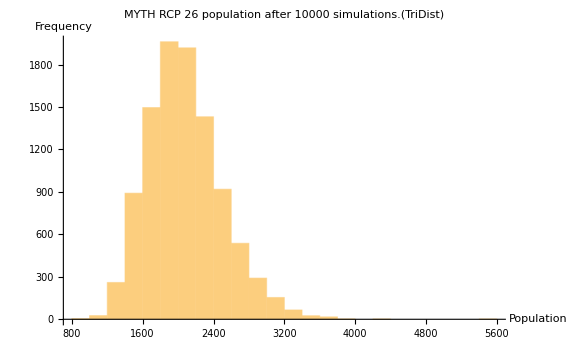

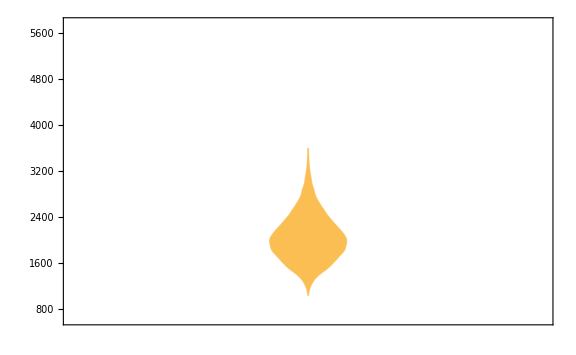

```mathematica
N[Mean[Round[MonteCarlo]]]
N[StandardDeviation[Round[MonteCarlo]]]
N[Min[Round[MonteCarlo]]]
N[Max[Round[MonteCarlo]]]
Hist=Round[MonteCarlo,50];
Histogram[Hist,BaseStyle->{FontSize->14},ImageSize->Large,PlotLabel->StringJoin["MYTH RCP 26 population after ",ToString[runs]," simulations.","(TriDist)"],AxesLabel->{"Population","Frequency"}]
DistributionChart[Round[MonteCarlo]]
```

## RCP 4.5 Projections and Simulations

### Model projections using RCP45 2009-2086 average values

Predicted probability of an adult female being reproductively active in a given year, given RCP45 average values for years 2009-2086, using logistic regression.

```mathematica
ProbRCP45Ave = {0.8500,0.8492,0.8485,0.8477,0.8470,0.8462,0.8455,0.8447,0.8440,0.8432,0.8425,0.8417,0.8410,0.8402,0.8395,0.8387,0.8380,0.8372,0.8365,0.8357,0.8350,0.8342,0.8335,0.8327,0.8320,0.8312,0.8305,0.8297,0.8290,0.8282,0.8274,0.8267,0.8259,0.8252,0.8244,0.8237,0.8229,0.8222,0.8214,0.8207,0.8199,0.8192,0.8184,0.8177,0.8169,0.8162,0.8154,0.8147,0.8139,0.8132,0.8124,0.8117,0.8109,0.8102,0.8094,0.8087,0.8079,0.8072,0.8064,0.8056,0.8049,0.8041,0.8034,0.8026,0.8019,0.8011,0.8004,0.7996,0.7989,0.7981,0.7974,0.7966,0.7959,0.7951,0.7944,0.7936,0.7929,0.7921};
Mean[ProbRCP45Ave]
```

0.821056

```mathematica
aReproRCP45Ave =ProbRCP45Ave;
```

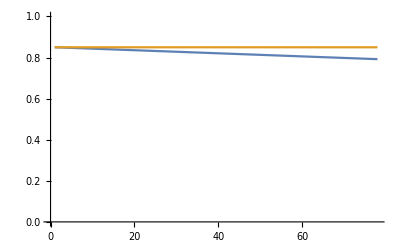

```mathematica
ListLinePlot[{aReproRCP45Ave, DetRepro},PlotRange->{0,1}]
```

### Monte Carlo RCP 45 simulation

```mathematica
SAave=0.79;
SAmin=SAave*0.90;
SAmax=SAave*1.10;

SFave=SAave*0.64;
SFmin=SFave*0.90;
SFmax=SFave*1.10;

aReproAve=SAave*(aReproRCP45Ave/2);
aReproMin=aReproAve*0.90;
aReproMax=aReproAve*1.10;

jReproAve=0.90*(aReproRCP45Ave/2)*SFave;
jReproMin=jReproAve*0.90;
jReproMax=jReproAve*1.10;

runs=10000;
j=0;
```

```mathematica
MonteCarlo=Table[Npups=600;Nne=290;Ntwo=230;Nthree=880;
i=1;While[i<77,Ntotal=Npups+Nne+Ntwo+Nthree;
Nthree=(Ntwo*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]))+(Nthree*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Ntwo=(Nne*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Nne=(Npups*(RandomReal[TriangularDistribution[{SFmin,SFmax},SFave]]));
Npups=(Npups*(RandomReal[TriangularDistribution[{jReproMin[[i]],jReproMax[[i]]},jReproAve[[i]]]]))+(Nne*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Ntwo*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Nthree*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]));
i=i+1;];j=j+1;Ntotal,{runs}];k=0;
```

1118.47

229.45

512.

2413.

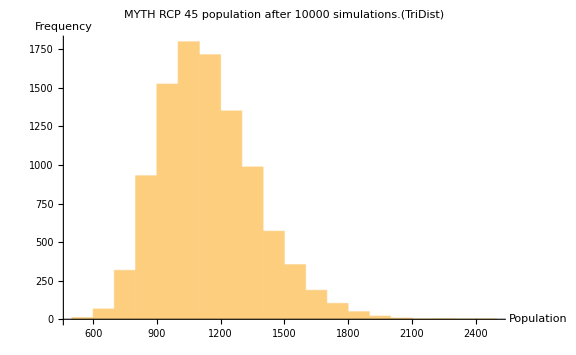

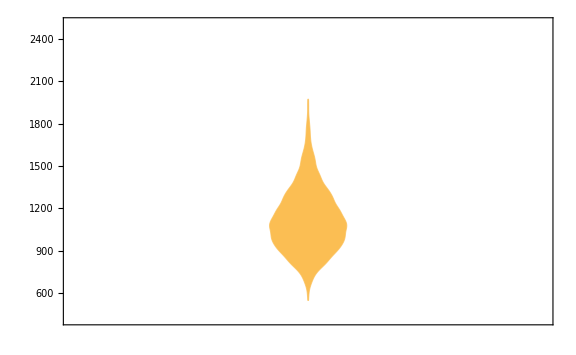

```mathematica
N[Mean[Round[MonteCarlo]]]
N[StandardDeviation[Round[MonteCarlo]]]
N[Min[Round[MonteCarlo]]]
N[Max[Round[MonteCarlo]]]
Hist=Round[MonteCarlo,50];
Histogram[Hist,BaseStyle->{FontSize->14},ImageSize->Large,PlotLabel->StringJoin["MYTH RCP 45 population after ",ToString[runs]," simulations.","(TriDist)"],AxesLabel->{"Population","Frequency"}]
DistributionChart[Round[MonteCarlo]]
```

## RCP 6.0

### Model projections using RCP60 2009-2086 average values

Predicted probability of an adult female being reproductively active in a given year, given RCP60 average values for years 2009-2086, using logistic regression:
Average RCP60 values for years 2009-2086 (from 1995, substract 15):

```mathematica
ProbRCP60Ave = {0.8500,0.8492,0.8485,0.8477,0.8469,0.8461,0.8454,0.8446,0.8438,0.8430,0.8423,0.8415,0.8407,0.8399,0.8392,0.8384,0.8376,0.8369,0.8361,0.8353,0.8345,0.8338,0.8330,0.8322,0.8314,0.8307,0.8299,0.8291,0.8283,0.8276,0.8268,0.8260,0.8253,0.8245,0.8237,0.8229,0.8222,0.8214,0.8206,0.8198,0.8191,0.8183,0.8175,0.8167,0.8160,0.8152,0.8144,0.8137,0.8129,0.8121,0.8113,0.8106,0.8098,0.8090,0.8082,0.8075,0.8067,0.8059,0.8051,0.8044,0.8036,0.8028,0.8021,0.8013,0.8005,0.7997,0.7990,0.7982,0.7974,0.7966,0.7959,0.7951,0.7943,0.7935,0.7928,0.7920,0.7912,0.7905};
Mean[ProbRCP60Ave]
```

0.820227

```mathematica
aReproRCP60Ave =ProbRCP60Ave;
```

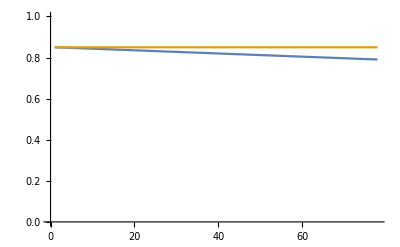

```mathematica
ListLinePlot[{aReproRCP60Ave,DetRepro},PlotRange->{0,1}]
```

### Monte Carlo RCP 60 simulation

```mathematica
SAave=0.79;
SAmin=SAave*0.90;
SAmax=SAave*1.10;

SFave=SAave*0.64;
SFmin=SFave*0.90;
SFmax=SFave*1.10;

aReproAve=SAave*(aReproRCP60Ave/2);
aReproMin=aReproAve*0.90;
aReproMax=aReproAve*1.10;

jReproAve=0.90*(aReproRCP60Ave/2)*SFave;
jReproMin=jReproAve*0.90;
jReproMax=jReproAve*1.10;

runs=10000;
j=0;
```

```mathematica
MonteCarlo=Table[Npups=600;Nne=290;Ntwo=230;Nthree=880;
i=1;While[i<77,Ntotal=Npups+Nne+Ntwo+Nthree;
Nthree=(Ntwo*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]))+(Nthree*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Ntwo=(Nne*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Nne=(Npups*(RandomReal[TriangularDistribution[{SFmin,SFmax},SFave]]));
Npups=(Npups*(RandomReal[TriangularDistribution[{jReproMin[[i]],jReproMax[[i]]},jReproAve[[i]]]]))+(Nne*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Ntwo*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Nthree*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]));
i=i+1;];j=j+1;Ntotal,{runs}];k=0;
```

1101.48

226.53

517.

2594.

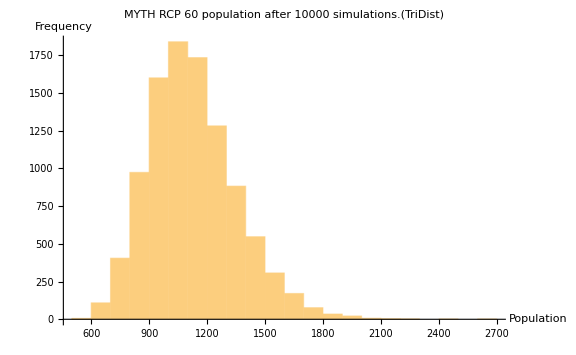

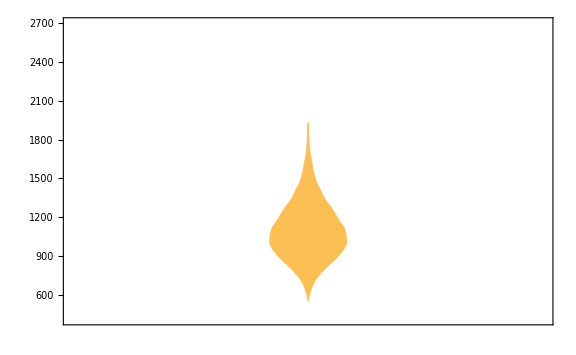

```mathematica
N[Mean[Round[MonteCarlo]]]
N[StandardDeviation[Round[MonteCarlo]]]
N[Min[Round[MonteCarlo]]]
N[Max[Round[MonteCarlo]]]
Hist=Round[MonteCarlo,50];
Histogram[Hist,BaseStyle->{FontSize->14},ImageSize->Large,PlotLabel->StringJoin["MYTH RCP 60 population after ",ToString[runs]," simulations.","(TriDist)"],AxesLabel->{"Population","Frequency"}]
DistributionChart[Round[MonteCarlo]]
```

## RCP 8.5

### Model projections using RCP85 2009-2086 average values

Predicted probability of an adult female being reproductively active in a given year, given RCP85 average values for years 2009-2086, using logistic regression:
Average RCP85 values for years 2009-2086 (from 1995, substract 15):

```mathematica
ProbRCP85Ave = {0.8500,0.8481,0.8461,0.8442,0.8422,0.8403,0.8383,0.8364,0.8345,0.8325,0.8306,0.8286,0.8267,0.8247,0.8228,0.8209,0.8189,0.8170,0.8150,0.8131,0.8111,0.8092,0.8073,0.8053,0.8034,0.8014,0.7995,0.7975,0.7956,0.7936,0.7917,0.7898,0.7878,0.7859,0.7839,0.7820,0.7800,0.7781,0.7762,0.7742,0.7723,0.7703,0.7684,0.7664,0.7645,0.7626,0.7606,0.7587,0.7567,0.7548,0.7528,0.7509,0.7490,0.7470,0.7451,0.7431,0.7412,0.7392,0.7373,0.7354,0.7334,0.7315,0.7295,0.7276,0.7256,0.7237,0.7218,0.7198,0.7179,0.7159,0.7140,0.7120,0.7101,0.7082,0.7062,0.7043,0.7023,0.7004};
Mean[ProbRCP85Ave]
```

0.775191

```mathematica
aReproRCP85Ave =ProbRCP85Ave;
```

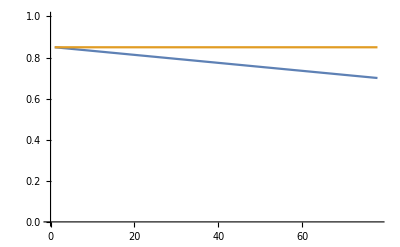

```mathematica
ListLinePlot[{aReproRCP85Ave, DetRepro},PlotRange->{0,1}]
```

### Monte Carlo RCP 85 simulation

```mathematica
SAave=0.79;
SAmin=SAave*0.90;
SAmax=SAave*1.10;

SFave=SAave*0.64;
SFmin=SFave*0.90;
SFmax=SFave*1.10;

aReproAve=SAave*(aReproRCP85Ave/2);
aReproMin=aReproAve*0.90;
aReproMax=aReproAve*1.10;

jReproAve=0.90*(aReproRCP85Ave/2)*SFave;
jReproMin=jReproAve*0.90;
jReproMax=jReproAve*1.10;

runs=10000;
j=0;
```

```mathematica
MonteCarlo=Table[Npups=600;Nne=290;Ntwo=230;Nthree=880;
i=1;While[i<77,Ntotal=Npups+Nne+Ntwo+Nthree;
Nthree=(Ntwo*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]))+(Nthree*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Ntwo=(Nne*(RandomReal[TriangularDistribution[{SAmin,SAmax},SAave]]));
Nne=(Npups*(RandomReal[TriangularDistribution[{SFmin,SFmax},SFave]]));
Npups=(Npups*(RandomReal[TriangularDistribution[{jReproMin[[i]],jReproMax[[i]]},jReproAve[[i]]]]))+(Nne*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Ntwo*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]))+(Nthree*(RandomReal[TriangularDistribution[{aReproMin[[i]],aReproMax[[i]]},aReproAve[[i]]]]));
i=i+1;];j=j+1;Ntotal,{runs}];k=0;
```

423.873

88.3709

153.

956.

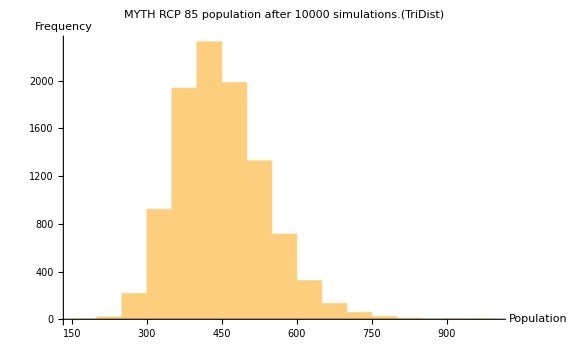

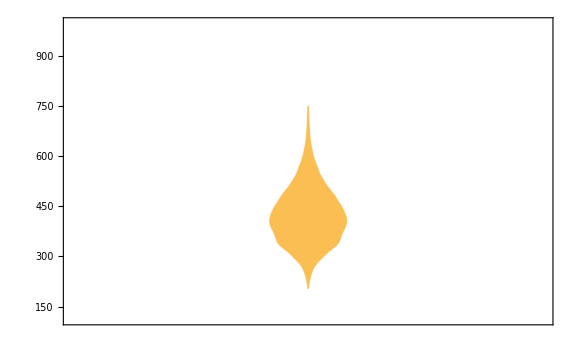

```mathematica
N[Mean[Round[MonteCarlo]]]
N[StandardDeviation[Round[MonteCarlo]]]
N[Min[Round[MonteCarlo]]]
N[Max[Round[MonteCarlo]]]
Hist=Round[MonteCarlo,50];
Histogram[Hist,BaseStyle->{FontSize->14},ImageSize->Large,PlotLabel->StringJoin["MYTH RCP 85 population after ",ToString[runs]," simulations.","(TriDist)"],AxesLabel->{"Population","Frequency"}]
DistributionChart[Round[MonteCarlo]]
```